### Data

```mathematica
dir="/Users/kouamano/Profile/"
```

/Users/kouamano/Profile/

```mathematica
xlsfile="01_24_2022-04_23_2022.xls"
```

01_24_2022-04_23_2022.xls

### Import

```mathematica
importData=Import[dir<>xlsfile];
```

```mathematica
selectedData[1]=Transpose[Transpose[Drop[importData[[1]],1]][[{1,3}]]];
```

```mathematica
ts=TimeSeries[selectedData[1]]
```

TimeSeries[…]

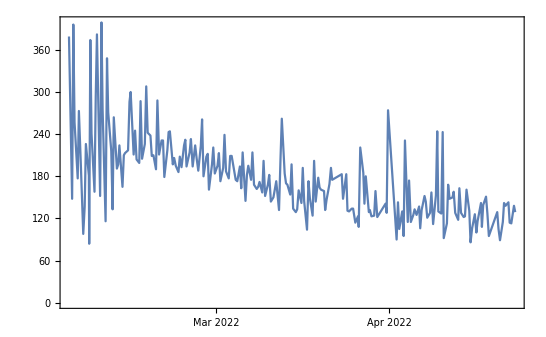

```mathematica
DateListPlot[ts]
```

### Interpolation

```mathematica
nts=Normal[ts];
```

```mathematica
nPts=Length[nts]
```

227

```mathematica
startDate=nts[[1,1]]
```

Wed 2 Feb 2022 16:45:00GMT+9

```mathematica
startTime=AbsoluteTime[nts[[1,1]]]
```

3852809100

```mathematica
endDate=nts[[-1,1]]
```

Sat 23 Apr 2022 11:53:00GMT+9

```mathematica
endTime=AbsoluteTime[nts[[-1,1]]]
```

3859703580

```mathematica
period=(endTime-startTime)/nPts//N
```

30372.2

```mathematica
endDate-startDate
```

79.7972 days

```mathematica
nPts/(endDate-startDate)
```

2.84471 per day

period 1

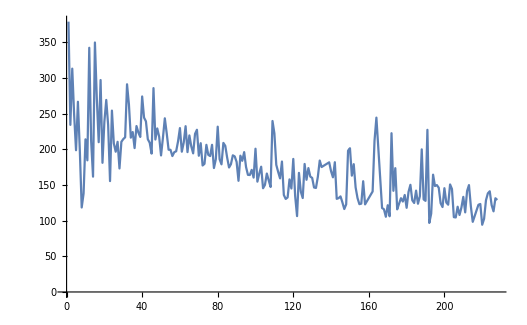

```mathematica
ListLinePlot[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]
```

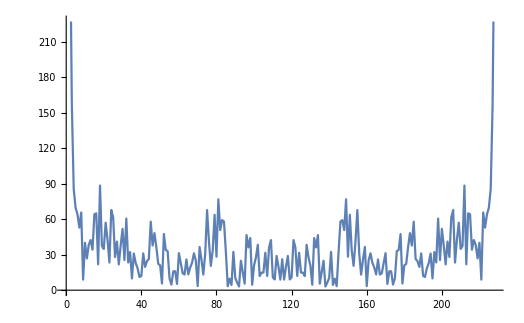

```mathematica
ListLinePlot[Fourier[Table[Interpolation[ts][t],{t,startTime,endTime,period}]]//Abs,PlotRange->{All,{0,nPts}}]
```

### SemanticImport

```mathematica
semanticData=SemanticImport[dir<>xlsfile]
```

```mathematica
semantic["date","glu"]=Map[{#[[1]],#[[3]]}&,semanticData]
```

```mathematica
semantic["date"]=Map[#[[1]]&,semanticData]
```

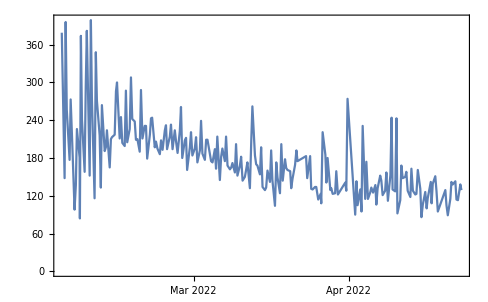

```mathematica
DateListPlot[semantic["date","glu"]]
```

```mathematica
semantic["date"]
```

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
AbsoluteTime[semantic["date"][[1]]]
```

3852809100

```mathematica
DateList[semantic["date"][[1]]]
```

{2022,2,2,16,45,0.}

```mathematica
AbsoluteTime[semantic["date"]]
```

AbsoluteTime::arg: 引数Dataset[«227»]は日付または時間入力として解釈することができません．

AbsoluteTime[]